```mathematica
SetOptions[EvaluationNotebook[],CellContext->Notebook];SetDirectory[NotebookDirectory[]];
```

```mathematica
(* Solve spherical black holes in the bumblebee gravity *)
```

## 1. Set up equations

```mathematica
n=4;coord={t,r,th,ph};schaf=1/(1-2*mass/r);schbf=1-2*mass/r;
```

```mathematica
metric0={{-Exp[2*nuf[r]],0,0,0},{0,Exp[2*muf[r]],0,0},{0,0,r^2,0},{0,0,0,r^2*(Sin[th])^2}};inversemetric0=Inverse[metric0];chris0=Simplify[Table[(1/2)*Sum[inversemetric0[[i,s]]*(D[metric0[[s,k]],coord[[j]]]+D[metric0[[j,s]],coord[[k]]]-D[metric0[[j,k]],coord[[s]]]),{s,1,n}],{i,1,n},{j,1,n},{k,1,n}]];riemann=Table[D[chris0[[i,j,ll]],coord[[k]]]-D[chris0[[i,j,k]],coord[[ll]]]+Sum[chris0[[i,k,s]]*chris0[[s,ll,j]]-chris0[[i,ll,s]]*chris0[[s,k,j]],{s,1,n}],{i,1,n},{j,1,n},{k,1,n},{ll,1,n}];ricci=Simplify[Table[Sum[riemann[[s,j,s,k]],{s,1,n}],{j,1,n},{k,1,n}]];riccis=Simplify[Sum[inversemetric0[[i,j]]*ricci[[i,j]],{i,1,n},{j,1,n}]];einstein=Simplify[Table[ricci[[i,j]]-1/2*metric0[[i,j]]*riccis,{i,1,n},{j,1,n}]];
```

```mathematica
bdown={btf[r],0,0,0};bbdown=Table[bdown[[i]]*bdown[[j]],{i,1,n},{j,1,n}];db=Table[D[bdown[[j]],coord[[i]]]-Sum[chris0[[s1,i,j]]*bdown[[s1]],{s1,1,n}],{i,1,n},{j,1,n}];bten=Table[db[[i,j]]-db[[j,i]],{i,1,n},{j,1,n}];dbb=Table[D[bbdown[[j,k]],coord[[i]]]-Sum[chris0[[s1,i,j]]*bbdown[[s1,k]]+chris0[[s1,i,k]]*bbdown[[j,s1]],{s1,1,n}],{i,1,n},{j,1,n},{k,1,n}];ddbb=Table[D[dbb[[i2,i3,i4]],coord[[i1]]]-Sum[chris0[[s1,i1,i2]]*dbb[[s1,i3,i4]]+chris0[[s1,i1,i3]]*dbb[[i2,s1,i4]]+chris0[[s1,i1,i4]]*dbb[[i2,i3,s1]],{s1,1,n}],{i1,1,n},{i2,1,n},{i3,1,n},{i4,1,n}];tbdown=Simplify[Table[xi*(1/2*metric0[[i,j]]*Sum[inversemetric0[[s1,s3]]*inversemetric0[[s2,s4]]*bbdown[[s1,s2]]*ricci[[s3,s4]],{s1,1,n},{s2,1,n},{s3,1,n},{s4,1,n}]-Sum[inversemetric0[[s1,s2]]*bbdown[[i,s1]]*ricci[[j,s2]]+inversemetric0[[s1,s2]]*bbdown[[j,s1]]*ricci[[i,s2]],{s1,1,n},{s2,1,n}]+1/2*(Sum[inversemetric0[[s1,s2]]*ddbb[[s1,i,s2,j]]+inversemetric0[[s1,s2]]*ddbb[[s1,j,s2,i]]-inversemetric0[[s1,s2]]*ddbb[[s1,s2,i,j]],{s1,1,n},{s2,1,n}]-metric0[[i,j]]*Sum[inversemetric0[[s1,s3]]*inversemetric0[[s2,s4]]*ddbb[[s1,s2,s3,s4]],{s1,1,n},{s2,1,n},{s3,1,n},{s4,1,n}]))+ka*(Sum[inversemetric0[[s1,s2]]*bten[[i,s1]]*bten[[j,s2]],{s1,1,n},{s2,1,n}]-1/4*metric0[[i,j]]*Sum[inversemetric0[[s1,s3]]*inversemetric0[[s2,s4]]*bten[[s1,s2]]*bten[[s3,s4]],{s1,1,n},{s2,1,n},{s3,1,n},{s4,1,n}]),{i,1,n},{j,1,n}]];
```

```mathematica
eeq=einstein-tbdown;
```

```mathematica
veceq=Simplify[Table[Sum[inversemetric0[[s1,s2]]*D[bten[[s2,i]],coord[[s1]]],{s1,1,n},{s2,1,n}]-Sum[inversemetric0[[s2,s3]]*(chris0[[s1,s2,s3]]*bten[[s1,i]]+chris0[[s1,s2,i]]*bten[[s3,s1]]),{s1,1,n},{s2,1,n},{s3,1,n}]+xi/ka*Sum[inversemetric0[[s1,s2]]*bdown[[s1]]*ricci[[s2,i]],{s1,1,n},{s2,1,n}],{i,1,n}]];
```

```mathematica
eqset={eeq[[1,1]],eeq[[2,2]],eeq[[3,3]],veceq[[1]]};eqsetab=Simplify[eqset/.{nuf[r]->(1/2)*Log[bf[r]],muf[r]->(1/2)*Log[af[r]],nuf'[r]->D[(1/2)*Log[bf[r]],r],muf'[r]->D[(1/2)*Log[af[r]],r],nuf''[r]->D[(1/2)*Log[bf[r]],r,r],muf''[r]->D[(1/2)*Log[af[r]],r,r]}];
```

```mathematica
case1asyiter0={mu0->0};case1asyiter1={nu1->-mu1};case1asyiter2={nu2->(b01^2 ka (ka-xi)-2 b00 b01 ka mu1 xi-2 mu1^2 (2 ⅇ^(2 nu0) ka+b00^2 xi (-ka+xi)))/(4 ⅇ^(2 nu0) ka+2 b00^2 xi (-2 ka+xi)),mu2->(ⅇ^(-2 nu0) (-b01^2 ka (2 ⅇ^(2 nu0) (ka-2 xi)+b00^2 (2 ka-xi) xi)+2 b00 b01 mu1 xi (6 ⅇ^(2 nu0) ka+b00^2 xi (-2 ka+xi))+2 mu1^2 (4 ⅇ^(4 nu0) ka+b00^4 xi^2 (-2 ka+xi)+2 b00^2 ⅇ^(2 nu0) xi (ka+xi))))/(4 (2 ⅇ^(2 nu0) ka+b00^2 xi (-2 ka+xi))),b02->-((b00 xi (2 b00 b01 mu1 xi+2 b00^2 mu1^2 xi+b01^2 (-ka+xi)))/(4 ⅇ^(2 nu0) ka+2 b00^2 xi (-2 ka+xi)))};case1asyiter3={nu3->(ⅇ^(-2 nu0) (8 b00 b01^3 ⅇ^(2 nu0) ka xi (2 ka^2-3 ka xi+xi^2)-2 b00 b01 mu1^2 xi (48 ⅇ^(4 nu0) ka^2-10 b00^2 ⅇ^(2 nu0) ka (2 ka-xi) xi+b00^4 xi^2 (-2 ka+xi)^2)+b01^2 ka mu1 (12 ⅇ^(4 nu0) ka (2 ka-3 xi)-b00^4 xi^2 (-2 ka+xi)^2+2 b00^2 ⅇ^(2 nu0) xi (-2 ka^2-5 ka xi+3 xi^2))-2 mu1^3 (32 ⅇ^(6 nu0) ka^2-16 b00^2 ⅇ^(4 nu0) ka (ka-2 xi) xi+b00^6 xi^3 (-2 ka+xi)^2+2 b00^4 ⅇ^(2 nu0) xi^2 (-2 ka^2-7 ka xi+4 xi^2))))/(12 (2 ⅇ^(2 nu0) ka+b00^2 xi (-2 ka+xi))^2),mu3->(ⅇ^(-2 nu0) (-24 b00 b01^3 ⅇ^(2 nu0) ka xi (2 ka^2-3 ka xi+xi^2)+6 b00 b01 mu1^2 xi (48 ⅇ^(4 nu0) ka^2-14 b00^2 ⅇ^(2 nu0) ka (2 ka-xi) xi+3 b00^4 xi^2 (-2 ka+xi)^2)-3 b01^2 ka mu1 (4 ⅇ^(4 nu0) ka (2 ka-7 xi)-3 b00^4 xi^2 (-2 ka+xi)^2+10 b00^2 ⅇ^(2 nu0) xi (2 ka^2-3 ka xi+xi^2))+2 mu1^3 (32 ⅇ^(6 nu0) ka^2+9 b00^6 xi^3 (-2 ka+xi)^2+16 b00^2 ⅇ^(4 nu0) ka xi (5 ka+2 xi)+2 b00^4 ⅇ^(2 nu0) xi^2 (-50 ka^2+17 ka xi+4 xi^2))))/(12 (2 ⅇ^(2 nu0) ka+b00^2 xi (-2 ka+xi))^2),b03->(ⅇ^(-2 nu0) xi (-8 b00^3 ⅇ^(2 nu0) mu1^3 xi (6 ⅇ^(2 nu0) ka+b00^2 xi (-2 ka+xi))+2 b00^2 b01 mu1^2 (4 ⅇ^(4 nu0) ka (2 ka-7 xi)+b00^4 xi^2 (-2 ka+xi)^2+2 b00^2 ⅇ^(2 nu0) xi (-6 ka^2+ka xi+xi^2))+2 b00 b01^2 mu1 (12 ⅇ^(4 nu0) ka (ka-xi)+b00^4 xi^2 (-2 ka+xi)^2+2 b00^2 ⅇ^(2 nu0) xi (-4 ka^2-4 ka xi+3 xi^2))+b01^3 (2 ka-xi) (4 ⅇ^(4 nu0) ka+b00^4 ka (2 ka-xi) xi-2 b00^2 ⅇ^(2 nu0) (ka^2-2 ka xi+3 xi^2))))/(12 (2 ⅇ^(2 nu0) ka+b00^2 xi (-2 ka+xi))^2)};nuasyexp=nu0+nu1/r+nu2/r^2+nu3/r^3+nu4/r^4;muasyexp=mu0+mu1/r+mu2/r^2+mu3/r^3+mu4/r^4;btasyexp=b00+b01/r+b02/r^2+b03/r^3+b04/r^4;
```

```mathematica
case1hbhiter0={af10->(rh (4 bf11+btf11^2 rh (2 ka-xi)))/(4 bf11)};case1hbhiter1={af11->1/(64 bf11^3 ka)(64 bf11^3 ka+3 btf11^6 rh^3 (2 ka-xi)^3 xi-4 bf11 btf11^4 rh^2 (ka-3 xi) (-2 ka+xi)^2)};case1hbhiter2={af12->1/(3072 bf11^5 ka^2)btf11^4 rh (-2 ka+xi)^2 (192 bf11^3 ka (ka-3 xi)+33 btf11^6 rh^3 (2 ka-xi)^3 xi^2-bf11 btf11^4 rh^2 (98 ka-237 xi) xi (-2 ka+xi)^2+4 bf11^2 btf11^2 rh (24 ka^3-280 ka^2 xi+344 ka xi^2-105 xi^3)),bf12->1/(16 bf11 ka rh)(-16 bf11^2 ka+4 bf11 btf11^2 ka rh (2 ka-xi)+btf11^4 rh^2 xi (-2 ka+xi)^2),btf12->1/(16 bf11^2 ka rh)(-16 bf11^2 btf11 ka+2 bf11 btf11^3 rh (2 ka-xi) xi+btf11^5 rh^2 xi (-2 ka+xi)^2)};case1hbhiter3={af13->-1/(49152 bf11^7 ka^3)btf11^4 (-2 ka+xi)^2 (3072 bf11^5 ka^2 (ka-3 xi)-126 btf11^10 rh^5 (2 ka-xi)^5 xi^3+3 bf11 btf11^8 rh^4 (194 ka-441 xi) xi^2 (-2 ka+xi)^4-2 bf11^2 btf11^6 rh^3 (2 ka-xi)^3 xi (366 ka^2-2691 ka xi+2282 xi^2)+8 bf11^3 btf11^4 rh^2 (-2 ka+xi)^2 (24 ka^3-758 ka^2 xi+1947 ka xi^2-644 xi^3)+128 bf11^4 btf11^2 ka rh (24 ka^3-244 ka^2 xi+326 ka xi^2-105 xi^3)),bf13->(768 bf11^4 ka^2-384 bf11^3 btf11^2 ka^2 rh (2 ka-xi)-48 bf11^2 btf11^4 ka rh^2 xi (-2 ka+xi)^2+6 btf11^8 rh^4 xi^2 (-2 ka+xi)^4+7 bf11 btf11^6 rh^3 (2 ka-xi)^3 xi (2 ka+3 xi))/(768 bf11^3 ka^2 rh^2),btf13->-((-768 bf11^4 btf11 ka^2+192 bf11^3 btf11^3 ka rh (2 ka-xi) xi+bf11 btf11^7 rh^3 (10 ka-33 xi) (2 ka-xi)^3 xi+12 bf11^2 btf11^5 rh^2 (10 ka-3 xi) xi (-2 ka+xi)^2-6 btf11^9 rh^4 xi^2 (-2 ka+xi)^4)/(768 bf11^4 ka^2 rh^2))};case1hbhiter4={af14->1/(11796480 bf11^9 ka^4 rh)(4 bf11+2 btf11^2 ka rh-btf11^2 rh xi) (737280 bf11^6 btf11^4 ka^6+737280 bf11^5 btf11^6 ka^7 rh+184320 bf11^4 btf11^8 ka^8 rh^2-2949120 bf11^6 btf11^4 ka^5 xi-10137600 bf11^5 btf11^6 ka^6 rh xi-8801280 bf11^4 btf11^8 ka^7 rh^2 xi-2224128 bf11^3 btf11^10 ka^8 rh^3 xi+2396160 bf11^6 btf11^4 ka^4 xi^2+23777280 bf11^5 btf11^6 ka^5 rh xi^2+46241280 bf11^4 btf11^8 ka^6 rh^2 xi^2+29867520 bf11^3 btf11^10 ka^7 rh^3 xi^2+6076160 bf11^2 btf11^12 ka^8 rh^4 xi^2-552960 bf11^6 btf11^4 ka^3 xi^3-21381120 bf11^5 btf11^6 ka^4 rh xi^3-85777920 bf11^4 btf11^8 ka^5 rh^2 xi^3-102193920 bf11^3 btf11^10 ka^6 rh^3 xi^3-44213760 bf11^2 btf11^12 ka^7 rh^4 xi^3-5890560 bf11 btf11^14 ka^8 rh^5 xi^3+8386560 bf11^5 btf11^6 ka^3 rh xi^4+77552640 bf11^4 btf11^8 ka^4 rh^2 xi^4+161074560 bf11^3 btf11^10 ka^5 rh^3 xi^4+115714560 bf11^2 btf11^12 ka^6 rh^4 xi^4+29890560 bf11 btf11^14 ka^7 rh^5 xi^4+1877760 btf11^16 ka^8 rh^6 xi^4-1209600 bf11^5 btf11^6 ka^2 rh xi^5-37333440 bf11^4 btf11^8 ka^3 rh^2 xi^5-140399040 bf11^3 btf11^10 ka^4 rh^3 xi^5-157554560 bf11^2 btf11^12 ka^5 rh^4 xi^5-63383040 bf11 btf11^14 ka^6 rh^5 xi^5-7511040 btf11^16 ka^7 rh^6 xi^5+9237600 bf11^4 btf11^8 ka^2 rh^2 xi^6+72153504 bf11^3 btf11^10 ka^3 rh^3 xi^6+126808800 bf11^2 btf11^12 ka^4 rh^4 xi^6+74457600 bf11 btf11^14 ka^5 rh^5 xi^6+13144320 btf11^16 ka^6 rh^6 xi^6-927360 bf11^4 btf11^8 ka rh^2 xi^7-21795600 bf11^3 btf11^10 ka^2 rh^3 xi^7-62933280 bf11^2 btf11^12 ka^3 rh^4 xi^7-53457600 bf11 btf11^14 ka^4 rh^5 xi^7-13144320 btf11^16 ka^5 rh^6 xi^7+3577800 bf11^3 btf11^10 ka rh^3 xi^8+19004480 bf11^2 btf11^12 ka^2 rh^4 xi^8+24151680 bf11 btf11^14 ka^3 rh^5 xi^8+8215200 btf11^16 ka^4 rh^6 xi^8-245700 bf11^3 btf11^10 rh^3 xi^9-3213480 bf11^2 btf11^12 ka rh^4 xi^9-6730080 bf11 btf11^14 ka^2 rh^5 xi^9-3286080 btf11^16 ka^3 rh^6 xi^9+233955 bf11^2 btf11^12 rh^4 xi^10+1060320 bf11 btf11^14 ka rh^5 xi^10+821520 btf11^16 ka^2 rh^6 xi^10-72450 bf11 btf11^14 rh^5 xi^11-117360 btf11^16 ka rh^6 xi^11+7335 btf11^16 rh^6 xi^12),bf14->1/(12288 bf11^5 ka^3 rh^3)(-12288 bf11^6 ka^3+3072 bf11^5 btf11^2 ka^3 rh (6 ka-3 xi)+15 btf11^12 rh^6 xi^3 (-2 ka+xi)^6+5 bf11 btf11^10 rh^5 (2 ka-xi)^5 xi^2 (2 ka+21 xi)-32 bf11^3 btf11^6 ka rh^3 (2 ka-xi)^3 xi (26 ka+21 xi)-2 bf11^2 btf11^8 rh^4 xi (-2 ka+xi)^4 (22 ka^2+81 ka xi-92 xi^2)),btf14->1/(12288 bf11^6 ka^3 rh^3)(-12288 bf11^6 btf11 ka^3+4608 bf11^5 btf11^3 ka^2 rh (2 ka-xi) xi+1728 bf11^4 btf11^5 ka rh^2 (2 ka-xi)^3 xi-5 bf11 btf11^11 rh^5 (10 ka-27 xi) (2 ka-xi)^5 xi^2+15 btf11^13 rh^6 xi^3 (-2 ka+xi)^6+8 bf11^3 btf11^7 rh^3 (2 ka-xi)^3 xi (72 ka^2-246 ka xi+37 xi^2)+2 bf11^2 btf11^9 rh^4 xi (-2 ka+xi)^4 (18 ka^2-293 ka xi+188 xi^2))};case1hbhiter5={bf15->-((-((-(144 bf11^2)/(rh^3 (4 bf11+btf11^2 rh (2 ka-xi))^2)+(36 bf11 btf11^2 (6 ka-3 xi))/(rh^2 (4 bf11+btf11^2 rh (2 ka-xi))^2)+(37 btf11^18 rh^6 (2 ka-xi)^9 xi^4)/(16384 bf11^7 ka^4 (4 bf11+btf11^2 rh (2 ka-xi))^2)-(5 btf11^16 rh^5 (538 ka-261 xi) xi^3 (-2 ka+xi)^8)/(49152 bf11^6 ka^4 (4 bf11+btf11^2 rh (2 ka-xi))^2)+(btf11^6 (2 ka-xi)^3 (12 ka^2-554 ka xi-21 xi^2))/(16 bf11 ka^2 (4 bf11+btf11^2 rh (2 ka-xi))^2)+(btf11^4 (2 ka-xi) (74 ka^2-79 ka xi+21 xi^2))/(ka rh (4 bf11+btf11^2 rh (2 ka-xi))^2)+(btf11^14 rh^4 (2 ka-xi)^7 xi^2 (5854 ka^2-21243 ka xi+3852 xi^2))/(36864 bf11^5 ka^4 (4 bf11+btf11^2 rh (2 ka-xi))^2)+(btf11^10 rh^2 (2 ka-xi)^5 (12 ka^3-1402 ka^2 xi+6459 ka xi^2-1172 xi^3))/(768 bf11^3 ka^3 (4 bf11+btf11^2 rh (2 ka-xi))^2)+(btf11^8 rh (-2 ka+xi)^4 (3 ka^3-203 ka^2 xi+174 ka xi^2+23 xi^3))/(16 bf11^2 ka^3 (4 bf11+btf11^2 rh (2 ka-xi))^2)+(btf11^12 rh^3 xi (-2 ka+xi)^6 (-1128 ka^3+18778 ka^2 xi-17517 ka xi^2+1269 xi^3))/(9216 bf11^4 ka^4 (4 bf11+btf11^2 rh (2 ka-xi))^2)) (-(40 bf11 btf11^2 (2 ka-xi)^2)/(ka rh^2 (4 bf11+btf11^2 rh (2 ka-xi))^2)+((320 bf11^2)/(rh (4 bf11+btf11^2 rh (2 ka-xi))^2)-(80 bf11 btf11^2 (-2 ka+xi))/((4 bf11+btf11^2 rh (2 ka-xi))^2))/rh^2))-(16 bf11^2 (1/(2 bf11)5 btf11 (2 ka-xi) (-(144 bf11^2 btf11 (2 ka-xi))/(ka rh^5 (4 bf11+btf11^2 rh (2 ka-xi))^2)-(5 btf11^17 rh^3 (202 ka-261 xi) (2 ka-xi)^9 xi^3)/(49152 bf11^6 ka^5 (4 bf11+btf11^2 rh (2 ka-xi))^2)-(52 bf11 btf11^3 (-2 ka+xi)^2)/(ka rh^4 (4 bf11+btf11^2 rh (2 ka-xi))^2)-(3 btf11^5 (ka-23 xi) (2 ka-xi) (-2 ka+xi)^2)/(ka^2 rh^3 (4 bf11+btf11^2 rh (2 ka-xi))^2)+(37 btf11^19 rh^4 xi^4 (-2 ka+xi)^10)/(16384 bf11^7 ka^5 (4 bf11+btf11^2 rh (2 ka-xi))^2)+(btf11^7 (-2 ka+xi)^4 (36 ka^2+1498 ka xi-1543 xi^2))/(48 bf11 ka^3 rh^2 (4 bf11+btf11^2 rh (2 ka-xi))^2)+(btf11^15 rh^2 xi^2 (-2 ka+xi)^8 (2254 ka^2-3783 ka xi+3852 xi^2))/(36864 bf11^5 ka^5 (4 bf11+btf11^2 rh (2 ka-xi))^2)-(btf11^13 rh (2 ka-xi)^7 xi (588 ka^3-1918 ka^2 xi-4938 ka xi^2-1269 xi^3))/(9216 bf11^4 ka^5 (4 bf11+btf11^2 rh (2 ka-xi))^2)+(btf11^9 (2 ka-xi)^5 (12 ka^3+198 ka^2 xi-1354 ka xi^2+387 xi^3))/(64 bf11^2 ka^4 rh (4 bf11+btf11^2 rh (2 ka-xi))^2)+(btf11^11 (-2 ka+xi)^6 (12 ka^3-272 ka^2 xi-2631 ka xi^2+3058 xi^3))/(768 bf11^3 ka^4 (4 bf11+btf11^2 rh (2 ka-xi))^2))-((320 bf11^2)/(rh (4 bf11+btf11^2 rh (2 ka-xi))^2)-(80 bf11 btf11^2 (-2 ka+xi))/((4 bf11+btf11^2 rh (2 ka-xi))^2)) (-4/rh^5+(7 btf11^2 (2 ka-xi))/(4 bf11 rh^4)+(37 btf11^18 rh^4 (2 ka-xi)^9 xi^4)/(262144 bf11^9 ka^4)-(5 btf11^16 rh^3 (202 ka-261 xi) xi^3 (-2 ka+xi)^8)/(786432 bf11^8 ka^4)+(btf11^6 (2 ka-xi)^3 (36 ka^2+38 ka xi-393 xi^2))/(768 bf11^3 ka^2 rh^2)-(3 btf11^4 (2 ka-xi) (2 ka^2-7 ka xi+3 xi^2))/(16 bf11^2 ka rh^3)+(btf11^14 rh^2 (2 ka-xi)^7 xi^2 (2254 ka^2-7653 ka xi+4257 xi^2))/(589824 bf11^7 ka^4)+(btf11^8 (-2 ka+xi)^4 (72 ka^3-182 ka^2 xi-1149 ka xi^2+652 xi^3))/(6144 bf11^4 ka^3 rh)+1/(589824 bf11^6 ka^4)btf11^12 rh xi (-2 ka+xi)^6 (-2352 ka^3+18532 ka^2 xi-19248 ka xi^2+8181 xi^3)+1/(49152 bf11^5 ka^4)btf11^10 (2 ka-xi)^5 (48 ka^4-1616 ka^3 xi+2716 ka^2 xi^2+1032 ka xi^3+505 xi^4))))/(4 bf11+btf11^2 rh (2 ka-xi))^2)/(-(25600 bf11^3)/(rh^2 (4 bf11+btf11^2 rh (2 ka-xi))^4)-(12800 bf11^2 btf11^2 ka)/(rh (4 bf11+btf11^2 rh (2 ka-xi))^4)+(6400 bf11^2 btf11^2 xi)/(rh (4 bf11+btf11^2 rh (2 ka-xi))^4))),btf15->1/(983040 bf11^8 ka^4 rh^4)btf11 (983040 bf11^8 ka^4-983040 bf11^7 btf11^2 ka^4 rh xi-1720320 bf11^6 btf11^4 ka^5 rh^2 xi-860160 bf11^5 btf11^6 ka^6 rh^3 xi-215040 bf11^4 btf11^8 ka^7 rh^4 xi-21504 bf11^3 btf11^10 ka^8 rh^5 xi+491520 bf11^7 btf11^2 ka^3 rh xi^2+2826240 bf11^6 btf11^4 ka^4 rh^2 xi^2+4300800 bf11^5 btf11^6 ka^5 rh^3 xi^2+2918400 bf11^4 btf11^8 ka^6 rh^4 xi^2+883200 bf11^3 btf11^10 ka^7 rh^5 xi^2+101120 bf11^2 btf11^12 ka^8 rh^6 xi^2-1536000 bf11^6 btf11^4 ka^3 rh^2 xi^3-5918720 bf11^5 btf11^6 ka^4 rh^3 xi^3-7654400 bf11^4 btf11^8 ka^5 rh^4 xi^3-4465920 bf11^3 btf11^10 ka^6 rh^5 xi^3-1248000 bf11^2 btf11^12 ka^7 rh^6 xi^3-134400 bf11 btf11^14 ka^8 rh^7 xi^3+276480 bf11^6 btf11^4 ka^2 rh^2 xi^4+3502080 bf11^5 btf11^6 ka^3 rh^3 xi^4+8776960 bf11^4 btf11^8 ka^4 rh^4 xi^4+8666240 bf11^3 btf11^10 ka^5 rh^5 xi^4+3972480 bf11^2 btf11^12 ka^6 rh^6 xi^4+806400 bf11 btf11^14 ka^7 rh^7 xi^4+53760 btf11^16 ka^8 rh^8 xi^4-944640 bf11^5 btf11^6 ka^2 rh^3 xi^5-5243520 bf11^4 btf11^8 ka^3 rh^4 xi^5-8688320 bf11^3 btf11^10 ka^4 rh^5 xi^5-6073280 bf11^2 btf11^12 ka^5 rh^6 xi^5-1881600 bf11 btf11^14 ka^6 rh^7 xi^5-215040 btf11^16 ka^7 rh^8 xi^5+94720 bf11^5 btf11^6 ka rh^3 xi^6+1672960 bf11^4 btf11^8 ka^2 rh^4 xi^6+4981472 bf11^3 btf11^10 ka^3 rh^5 xi^6+5304000 bf11^2 btf11^12 ka^4 rh^6 xi^6+2352000 bf11 btf11^14 ka^5 rh^7 xi^6+376320 btf11^16 ka^6 rh^8 xi^6-260480 bf11^4 btf11^8 ka rh^4 xi^7-1655920 bf11^3 btf11^10 ka^2 rh^5 xi^7-2802960 bf11^2 btf11^12 ka^3 rh^6 xi^7-1764000 bf11 btf11^14 ka^4 rh^7 xi^7-376320 btf11^16 ka^5 rh^8 xi^7+14160 bf11^4 btf11^8 rh^4 xi^8+297880 bf11^3 btf11^10 ka rh^5 xi^8+890600 bf11^2 btf11^12 ka^2 rh^6 xi^8+823200 bf11 btf11^14 ka^3 rh^7 xi^8+235200 btf11^16 ka^4 rh^8 xi^8-22480 bf11^3 btf11^10 rh^5 xi^9-157140 bf11^2 btf11^12 ka rh^6 xi^9-235200 bf11 btf11^14 ka^2 rh^7 xi^9-94080 btf11^16 ka^3 rh^8 xi^9+11865 bf11^2 btf11^12 rh^6 xi^10+37800 bf11 btf11^14 ka rh^7 xi^10+23520 btf11^16 ka^2 rh^8 xi^10-2625 bf11 btf11^14 rh^7 xi^11-3360 btf11^16 ka rh^8 xi^11+210 btf11^16 rh^8 xi^12)};bhbhexp=bf11*de+bf12*de^2+bf13*de^3+bf14*de^4+bf15*de^5+bf16*de^6;ahbhexp=de^-1*(af10+af11*de+af12*de^2+af13*de^3+af14*de^4+af15*de^5+af16*de^6);bthbhexp=btf11*de+btf12*de^2+btf13*de^3+btf14*de^4+btf15*de^5+btf16*de^6;bhbhpexp=D[bhbhexp,de];ahbhpexp=D[ahbhexp,de];bthbhpexp=D[bthbhexp,de];{bhbhexp1,ahbhexp1,bthbhexp1,bhbhpexp1,ahbhpexp1,bthbhpexp1}=Simplify[{bhbhexp,ahbhexp,bthbhexp,bhbhpexp,ahbhpexp,bthbhpexp}/.case1hbhiter0/.case1hbhiter1/.case1hbhiter2/.case1hbhiter3/.{bf14->0,af14->0,btf14->0,bf15->0,af15->0,btf15->0,bf16->0,af16->0,btf16->0}];{bhbhexp2,ahbhexp2,bthbhexp2,bhbhpexp2,ahbhpexp2,bthbhpexp2}=Simplify[{bhbhexp,ahbhexp,bthbhexp,bhbhpexp,ahbhpexp,bthbhpexp}/.case1hbhiter0/.case1hbhiter1/.case1hbhiter2/.{bf13->0,af13->0,btf13->0,bf14->0,af14->0,btf14->0,bf15->0,af15->0,btf15->0,bf16->0,af16->0,btf16->0}];
```

```mathematica
lreq=gttp/(2*gtt)-1/r;iscoeq=gttpp-(2*gttp^2)/gtt+(3*gttp)/r;sigma=r/Sqrt[-gtt];{iscoepsq,iscolsq}={(-2*gtt)/r*1/(2/r-gttp/gtt),(r^2*gttp/gtt)/(2/r-gttp/gtt)};{ursq,ar}={-epsq/(gtt*grr)-lsq/(r^2*grr)+sign/grr,epsq/(2*gtt*grr)*(gttp/gtt+grrp/grr)+lsq/(r^2*grr)*(grrp/(2*grr)+1/r)-sign*grrp/(2*grr^2)};{lreq1,iscoeq1,sigma1,iscoepsq1,iscolsq1,ursq1,ar1}=Simplify[{lreq,iscoeq,sigma,iscoepsq,iscolsq,ursq,ar}/.{gtt->metric0[[1,1]],gttp->D[metric0[[1,1]],r],gttpp->D[metric0[[1,1]],r,r],grr->metric0[[2,2]],grrp->D[metric0[[2,2]],r]}];{lreq2,iscoeq2,sigma2,iscoepsq2,iscolsq2,ursq2,ar2}=Simplify[{lreq1,iscoeq1,sigma1,iscoepsq1,iscolsq1,ursq1,ar1}/.{nuf[r]->1/2*Log[bf[r]],muf[r]->1/2*Log[af[r]],nuf'[r]->D[1/2*Log[bf[r]],r],muf'[r]->D[1/2*Log[af[r]],r],nuf''[r]->D[1/2*Log[bf[r]],r,r],muf''[r]->D[1/2*Log[af[r]],r,r]}];{lreqgr,iscoeqgr,sigmagr,iscoepsqgr,iscolsqgr,ursqgr,argr}=Simplify[{lreq,iscoeq,sigma,iscoepsq,iscolsq,ursq,ar}/.{gtt->-schbf,gttp->D[-schbf,r],gttpp->D[-schbf,r,r],grr->schaf,grrp->D[schaf,r]}];xydotsol={rdot*Cos[ph]+r*(-Sin[ph])*phdot,rdot*Sin[ph]+r*(Cos[ph])*phdot};eplsqsol={epsq,lsq}/.Solve[{ursq==rdot^2,(r^2*phdot)^2==lsq},{epsq,lsq}][[1]];eplsqsol1=eplsqsol/.{gtt->metric0[[1,1]],gttp->D[metric0[[1,1]],r],grr->metric0[[2,2]],grrp->D[metric0[[2,2]],r]};eplsqsol2=eplsqsol1/.{nuf[r]->1/2*Log[bf[r]],muf[r]->1/2*Log[af[r]],nuf'[r]->D[1/2*Log[bf[r]],r],muf'[r]->D[1/2*Log[af[r]],r],nuf''[r]->D[1/2*Log[bf[r]],r,r],muf''[r]->D[1/2*Log[af[r]],r,r]};
```

```mathematica
kanum1=8*Pi;rhnum1=1;bf11num1=10.;bumbhsolversim[par1_,par2_]:=Module[{flag=0,denum1=10^-8,rinfnum1=10000,btf11num1=par2,xinum1=par1*kanum1,eqsetabnum,bhnum1,ahnum1,bthnum1,bhpnum1,ahpnum1,bthpnum1,case1solh1,aftest,rnum1,rnum2,denum2,npt,xdata,ydata,bhfit,ahfit,bthfit,ah0fit,ah1fit,ah2fit,bh1fit,bh2fit,bth1fit,bth2fit,errh=0,rinfnum2,rinfnum3,fitint1,fitint2,testnpt1,testnpt2,testx,testy,testerr,rfitnum1=0,rfitnum2=0,nuasyfit,muasyfit,btasyfit,nu0num2=0,nu1num2,nu2num2,mu1num2=0,mu2num2,b00num2,b01num2=0,b02num2,errasy=0,lreq2num,rlnum=0,sigmanum=0,pritest},pritest=af10/.case1hbhiter0/.{ka->kanum1,xi->xinum1,rh->rhnum1,de->denum1,bf11->bf11num1,btf11->btf11num1};If[pritest<=10^-8,,eqsetabnum=eqsetab/.{ka->kanum1,xi->xinum1};{bhnum1,ahnum1,bthnum1,bhpnum1,ahpnum1,bthpnum1}={bhbhexp1,ahbhexp1,bthbhexp1,bhbhpexp1,ahbhpexp1,bthbhpexp1}/.{ka->kanum1,xi->xinum1,rh->rhnum1,de->denum1,bf11->bf11num1,btf11->btf11num1};case1solh1=NDSolve[{eqsetabnum[[1]]==0,eqsetabnum[[3]]==0,eqsetabnum[[4]]==0,bf[rhnum1+denum1]==bhnum1,bf'[rhnum1+denum1]==bhpnum1,af[rhnum1+denum1]==ahnum1,btf[rhnum1+denum1]==bthnum1,btf'[rhnum1+denum1]==bthpnum1},{bf,af,btf},{r,rhnum1+denum1,rinfnum1}];aftest=af/.case1solh1[[1]];{rnum1,rnum2}=aftest["Domain"][[1]];If[rnum2>0.99*rinfnum1,flag=1;denum2=0.01;npt=100;xdata=Table[denum1+(i-1)*(denum2-denum1)/(npt-1),{i,1,npt}];ydata=Table[{bf[xdata[[i]]+rhnum1]/.case1solh1[[1]],af[xdata[[i]]+rhnum1]/.case1solh1[[1]],btf[xdata[[i]]+rhnum1]/.case1solh1[[1]]},{i,1,npt}];bhfit=Fit[Table[{xdata[[i]],ydata[[i,1]]},{i,1,npt}],{x,x^2},x];ahfit=Fit[Table[{xdata[[i]],ydata[[i,2]]},{i,1,npt}],{x^-1,1,x^1},x];bthfit=Fit[Table[{xdata[[i]],ydata[[i,3]]},{i,1,npt}],{x,x^2},x];{ah0fit,ah1fit,ah2fit,bh1fit,bh2fit,bth1fit,bth2fit}={Coefficient[ahfit,x,-1],Coefficient[ahfit,x,0],Coefficient[ahfit,x,1],Coefficient[bhfit,x,1],Coefficient[bhfit,x,2],Coefficient[bthfit,x,1],Coefficient[bthfit,x,2]};errh=Min[Abs[{1-ah2fit/af12,1-bh2fit/bf12,1-bth2fit/btf12}/.case1hbhiter2/.case1hbhiter1/.case1hbhiter0/.{ka->kanum1,xi->xinum1,rh->rhnum1,bf11->bf11num1,btf11->btf11num1}]];rfitnum2=250;rfitnum1=200;npt=50;xdata=Table[rfitnum1+(i-1)*(rfitnum2-rfitnum1)/(npt-1),{i,1,npt}];ydata=Table[{1/2*Log[bf[xdata[[i]]]]/.case1solh1[[1]],1/2*Log[af[xdata[[i]]]]/.case1solh1[[1]],btf[xdata[[i]]]/.case1solh1[[1]]},{i,1,npt}];nuasyfit=Fit[Table[{xdata[[i]],ydata[[i,1]]},{i,1,npt}],{1,x^-1,x^-2},x];muasyfit=Fit[Table[{xdata[[i]],ydata[[i,2]]},{i,1,npt}],{x^-1,x^-2},x];btasyfit=Fit[Table[{xdata[[i]],ydata[[i,3]]},{i,1,npt}],{1,x^-1,x^-2},x];{nu0num2,nu1num2,mu1num2,b00num2,b01num2}={Coefficient[nuasyfit,x,0],Coefficient[nuasyfit,x,-1],Coefficient[muasyfit,x,-1],Coefficient[btasyfit,x,0],Coefficient[btasyfit,x,-1]};lreq2num[r_]=lreq2/.case1solh1[[1]];rlnum=r/.FindRoot[lreq2num[r]==0,{r,rhnum1+0.1}];sigmanum=Exp[nu0num2]*sigma2/.case1solh1[[1]]/.r->rlnum;If[errh<0.1,flag=2]]];Return[{flag,mu1num2,-Sqrt[4*Pi]*b01num2*Exp[-nu0num2],errh,rlnum,sigmanum,par1,par2}]];
```

## 2. Numerical solution

### 2.1 Input the value for the coupling constant

```mathematica
xinum=-1.35;
```

### 2.2 Solve and record data

```mathematica
npt2=100;{btf11min,btf11max}={0.001,10};btf11set=Table[N[Exp[Log[btf11min]+(ii-1)*(Log[btf11max]-Log[btf11min])/(npt2-1)]],{ii,1,npt2}];If[xinum>2,btfupnum=(2 √bf11)/(√(-2 ka rh+rh xi))/.{xi->xinum*ka}/.{rh->rhnum1,bf11->bf11num1,ka->kanum1};btfupnum1=btfupnum;debtfupnum1=0.001;btf11set=Table[N[btfupnum1+debtfupnum1-Exp[Log[btfupnum1-btf11min]+(ii-1)*(Log[debtfupnum1]-Log[btfupnum1-btf11min])/(npt2-1)]],{ii,1,npt2}];]
```

```mathematica
testres=Table[0,{k,1,6},{j,1,npt2}];jcut1=npt2;Do[res=Block[{par1=xinum,par2=btf11set[[j]]},bumbhsolversim[par1,par2]];testres[[1,j]]=res[[1]];testres[[2,j]]=res[[2]];testres[[3,j]]=res[[3]];testres[[4,j]]=res[[4]];testres[[5,j]]=res[[5]];testres[[6,j]]=res[[6]];If[res[[2]]==0,jcut1=j-1;Break[]],{j,1,npt2}];jcut1
```

100

```mathematica
Export[StringJoin["bumblebeebh_data.txt"],Table[{testres[[3,i]]/testres[[2,i]],1/testres[[2,i]],testres[[5,i]]/testres[[2,i]],testres[[6,i]]/testres[[2,i]]},{i,1,jcut1}],"Table"]
```

bumblebeebh_data.txt

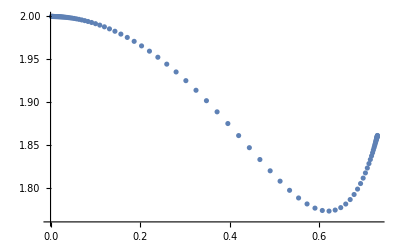

```mathematica
ListPlot[Table[{testres[[3,i]]/testres[[2,i]],1/testres[[2,i]]},{i,1,jcut1}]]
```

```mathematica
TimeUsed[]
```

4.8849